```mathematica
SetDirectory["~/Dropbox/PMB/PMBModel/Runs"];

(*vector of dispersal rates (probability of moving per day per adult)*)
dli=0.02Table[5^i,{i,-1,1,0.5}];
dli={0.02};
(*Function giving lifetime probability of dispersing, if mortality is mu and dispersal rate is p*)
pdisp[mu_,p_]:=p(1-mu)/(mu+p-mu p);
(*-------------------------------------------------------------------*)
(*corresponding vector of lifetime probability to move, if daily mortality is 0.125*)
Print[Map[pdisp[0.125,#]&,dli]];
(*-------------------------------------------------------------------*)
(*vector of fitness cots*)
xili={0.6,0.9};
(*-------------------------------------------------------------------*)
(*vector of values for carrying capacity parameter*)
allis=Table[i,{i,1000,9000,2000}];
allis={50000};
```

{0.122807}

```mathematica
Do[input={"../InputData/Rel2Vil.txt"}[[size]];
pa=Flatten[{numruns=1,maxT=25 365+200,NumPat={726}[[size]],muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,bias=0.9,omegaM=xili[[xx]],omegaF=xili[[xx]],drivertime=25 365+150,NumDriver=1000,NumDriverPat=1,d=dli[[dd]],L=5/111.(*5km maximum dispersal distance*),psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,allis[[a0]],al0var=0.,allis[[a1]] ,amp=0,resp=.25,recstart=24 365,recend=maxT,recIntGlob=1,recIntLoc=1,recsitesfreq=1,set=100000a0+10000a1+1000 size+100 rel+10 (xx)+dd,"e","r",start=24 365,input,"../InputData/IslandRain.csv",{"../InputData/Rellist.csv","../InputData/RellistSingle.csv"}[[rel]],"../InputData/ConsMort.csv",outputtype=3}];
Export["Pars"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{rel,1},{size,{1}},{xx,Length[xili]},{dd,Length[dli]},{a0,Length[allis]},{a1,Length[allis]}];
```

```mathematica
out=Import["!../build/gdsimsapp<Pars"<>ToString[set]<>".csv","Table"];
```

```mathematica
tot=Drop[Import["./output_files/Totals"<>ToString[set-10]<>"run1.txt","Table"],2];
Dimensions[tot]
```

{201,4}

```mathematica
Table[50000 .875^i,{i,5}]
```

{43750.,38281.3,33496.1,29309.1,25645.4}

```mathematica
Last[tot]
```

{8910,0,0,0}

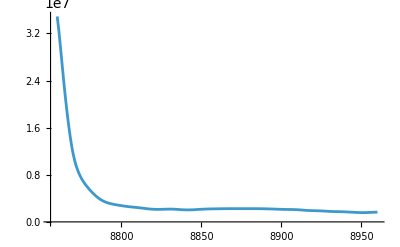

```mathematica
ListLinePlot[tot[[All,{1,2}]],PlotRange->All]
```

```mathematica
set
```

111121

```mathematica
out[[1;;10]]
```

{}